```mathematica
Get["Bfield+Drift/Drifts.m"]
```

(alpha p q (2-rRxB Sin[th0]^2))/(599584916 BRxB (1-G1 (yRxBGC-YRxBShift)+G2 (yRxBGC-YRxBShift)^2) √(1-rRxB Sin[th0]^2))-(1.54642×10^-27 alpha^3 p^3 q^3 (2-rRxB Sin[th0]^2)^3)/(BRxB^3 (R+yRxBGC)^2 (1-G1 (yRxBGC-YRxBShift)+G2 (yRxBGC-YRxBShift)^2)^3 (1-rRxB Sin[th0]^2)^(3/2))

```mathematica
?BpolynomGradwoR
```

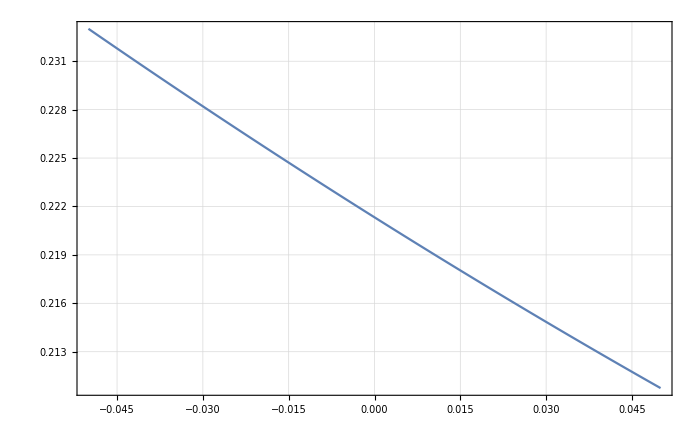

```mathematica
Plot[BpolynomGradwoR[y0,0.006,0.22,1,1],{y0,-0.05,+0.05}]
```

```mathematica
?pminCases
```

Global`pminCases

pminCases[x0_,x_,thD_,BD_,alpha_,th0_,rRxB_,BRxB_]:=Which[pminFunc[x0,x,thD,BD,alpha,th0,rRxB,BRxB]>pmax,pmax,pminFunc[x0,x,thD,BD,alpha,th0,rRxB,BRxB]<0,0,True,pminFunc[x0,x,thD,BD,alpha,th0,rRxB,BRxB]]

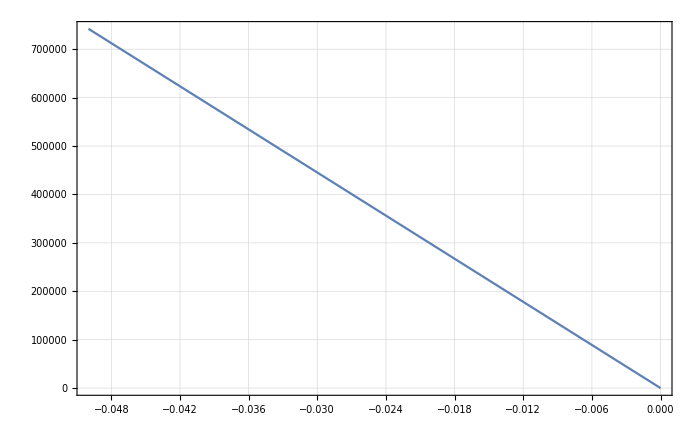

```mathematica
Plot[pminCases[0.,x,45/180*Pi,0.2,Pi,45/180*Pi,1,0.2],{x,-0.05,0}]
```

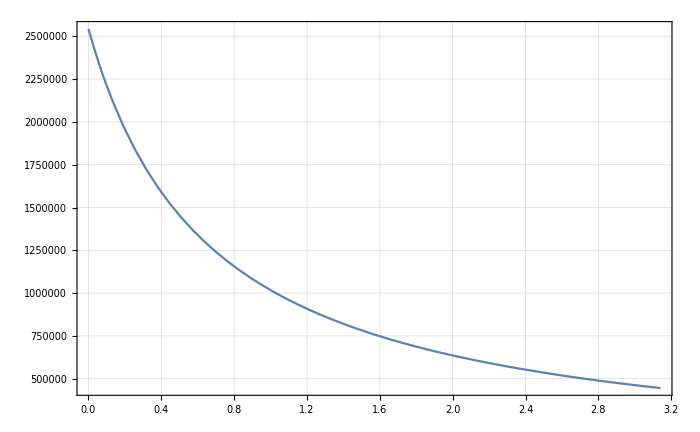

```mathematica
Plot[pminFunc[0.,-0.03,45/180*Pi,0.2,alpha,45/180*Pi,1,0.2],{alpha,0,Pi}]
```

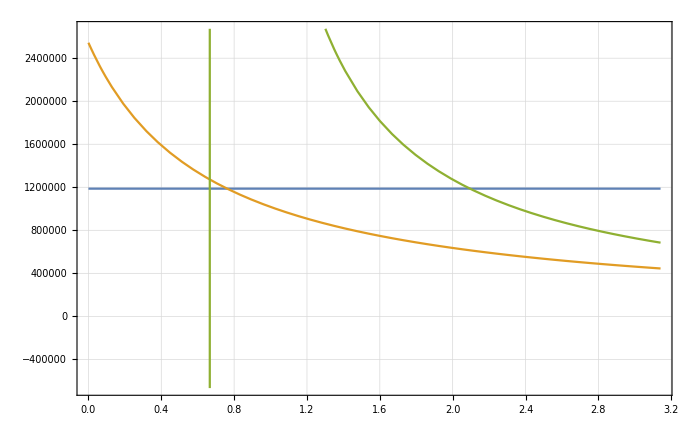

```mathematica
Plot[{pmax,pminFunc[0.,-0.03,45/180*Pi,0.2,alpha,45/180*Pi,1,0.2],pmaxFunc[0.,-0.03,45/180*Pi,0.2,alpha,45/180*Pi,1,0.2]},{alpha,0,Pi}]
```

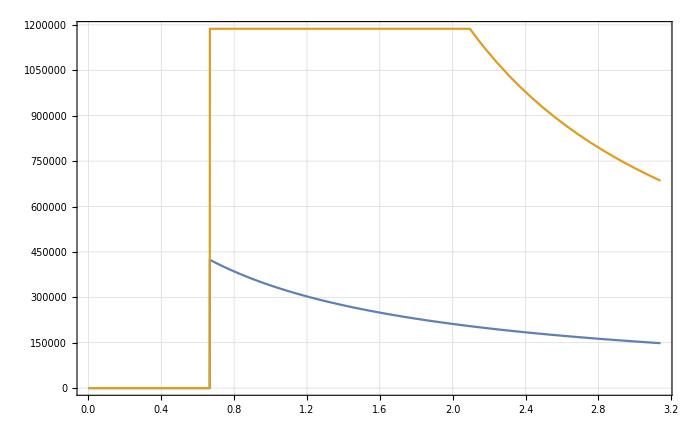

```mathematica
Plot[{pminCases[0.,-0.01,45/180*Pi,0.2,alpha,45/180*Pi,1,0.2],pmaxCases[0.,-0.03,45/180*Pi,0.2,alpha,45/180*Pi,1,0.2]},{alpha,0,Pi}]
```

```mathematica
{p,Sequence@@{a,b}}
```

{p,a,b}

```mathematica
pminCases[0.,-0.03,45/180*Pi,0.2,0,45/180*Pi,1,0.2]
```

1.18728×10^6

```mathematica
pmaxCases[0.,-0.03,45/180*Pi,0.2,0,45/180*Pi,1,0.2]
```

0

```mathematica
?pmaxFunc
```

Global`pmaxFunc

pmaxFunc[x0_,x_,thD_,BD_,alpha_,th0_,rRxB_,BRxB_]:=(x-x0)/(Sin[thD]/(c BD)-(alpha fReduced[th0,rRxB])/(c BRxB))

```mathematica
pmaxFunc[0.,-0.03,45/180*Pi,0.2,0,45/180*Pi,1,0.2]
```

-2.54382×10^6

```mathematica
pminFunc[0.,-0.03,45/180*Pi,0.2,0,45/180*Pi,1,0.2]
```

2.54382×10^6